## Generating mesh with periodic boundary condition

```mathematica
(* subdividing XY grid *)
```

```mathematica
xL= 13.20;yL=15.20;cellNumX=20;
```

```mathematica
{δx,δy}=Part[Subdivide[0,#,cellNumX-1],2]&/@{xL,yL};
```

```mathematica
{x,y,z}=Transpose@Flatten[Table[{x,y,0.5*Cos[2π x/xL]Cos[2π y/yL]},{x,0,xL,δx},{y,0,yL,δy}],1];
threadedPts=Thread[{x,y,z}];
cols=ColorData["Rainbow"]/@Rescale[z];
Print[Style["# of cells in the grid : ",Blue,Bold],Length@threadedPts];
```

# of cells in the grid : 400

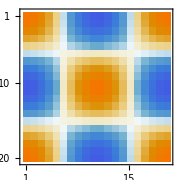
-Graphics3D- | -Graphics-

```mathematica
Grid[{{Graphics3D[{PointSize[0.017],Thread[{cols,Point/@threadedPts}]},Axes->True,AxesLabel->{"x","y","z"},ImageSize->Medium],
MatrixPlot[Partition[z,cellNumX],ImageSize->Small]}}] (* grid pts and z coordinate value in the grid represented as matrixplot *)
```

```mathematica
AllTrue[Through[{First,Last}[#]]&/@Partition[z,cellNumX],SameQ] 
AllTrue[Through[{First,Last}[#]]&/@(Partition[z,cellNumX])ᵀ,SameQ]
(* Z coordinates at the edges are the same along X & Y Axes *)
```

True

True

```mathematica
(* initial seed for a hexagon face *)
circlepts=0.45CirclePoints[{1,1},{1,0},6];
pts=Reverse[NestList[{0,0.45Sqrt[3]}+#&/@#&,circlepts,cellNumX-1],{3}];
```

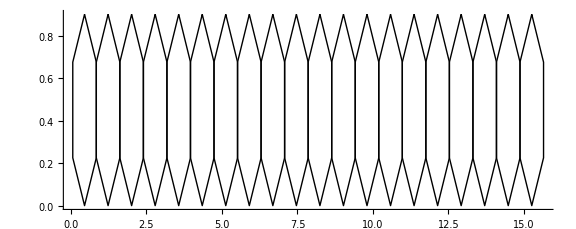

```mathematica
Graphics[{Black,Thick,Line[#~Append~First[#]]&/@pts},Axes->True,ImageSize->Large]
```

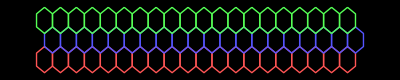

```mathematica
Block[{col2,col3},
col2=Map[0.45{Sqrt[3]/2,3/2}+#&,pts,{2}];
col3=Map[0.45{-Sqrt[3]/2,3/2}+#&,col2,{2}];
Show[{Graphics[{Thick,Lighter@Red,Line[#~Append~First[#]]&/@pts}],
Graphics[{Thick,Lighter@Blue,Line[#~Append~First[#]]&/@col2}],
Graphics[{Thick,Lighter@Green,Line[#~Append~First[#]]&/@col3}]},
Background->Black]
]
```

### getting a hexagonal lattice

```mathematica
(* We generate a 2D hexagonal grid; Add a mirror Z plane; Make pairs and Construct Polyhedra *)
```

```mathematica
grid=Block[{temp,k=1,p=cellNumX},
NestList[(temp=Map[x↦0.45{If[OddQ[k],-1,1] (Sqrt[3]/2),3/2}+x,#,{2}];k++;
temp)&,pts,p-1]
];
```

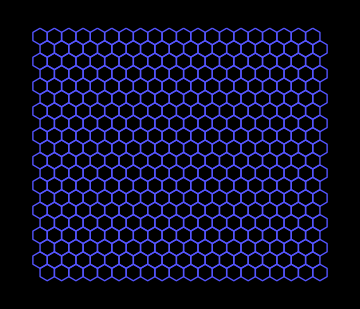

```mathematica
Graphics[{Thick,Lighter@Blue,Map[Line[#~Append~First[#]]&,grid,{2}]},Background->Black,ImageSize->Medium]
```

```mathematica
xyzPts=Table[{Last[i],First[i],(0.5)*Cos[2π Last[i]/xL]Cos[2π First[i]/yL]},{i,Flatten[grid,2]}];
(*adding Z coordinate (height) to the polgonal face *)
```

```mathematica
Graphics3D[{Point@DeleteDuplicates@xyzPts},ImageSize->Medium]
```

-Graphics3D-

```mathematica
nf=Nearest[DeleteDuplicates@xyzPts]
```

NearestFunction[…]

```mathematica
(nf[#,{All,1.0 10^-15}]&/@DeleteDuplicates[xyzPts])//Counts@*Map[Length] (* # of pts for which keys are > 1 need merging because of 
very tiny numerical errors. All this could have been avoided in the first place *)
```

<|3→57,2→498,1→612|>

```mathematica
replacements=Dispatch@Flatten@
Map[Function[x,#-> Mean[x]&/@x],
SortBy[Cases[Gather[DeleteDuplicates@xyzPts,EuclideanDistance[#1,#2]≤ 1.0 10^-15&],x_/;Length[x]>1],
First]
]
```

Dispatch[…]

```mathematica
(*replacements=Dispatch@Flatten[(x↦First[x]-> #&/@Rest[x])/@Cases[Gather[DeleteDuplicates@Flatten[grid,2],EuclideanDistance[#1,#2]≤ 1.0 10^-15&],
x_/;Length[x]>1],1]*)
```

```mathematica
xyzPts=xyzPts/.replacements;
```

```mathematica
Print[Length@DeleteDuplicates@xyzPts]
Graphics3D[Point@DeleteDuplicates@xyzPts,ImageSize->Medium]
```

880

-Graphics3D-

```mathematica
nf=Nearest[DeleteDuplicates@xyzPts]
```

NearestFunction[…]

```mathematica
Apply[And]//@(Map[Through[{Apply[SameQ],Apply[Equal]}[#]]&]@Cases[
nf[#,{All,1.0 10^-15}]&/@DeleteDuplicates[xyzPts],
x_/;Length[x]>1])(*if value is true then the polygons have successfully shared common vertices *)
```

True

```mathematica
XYZgrid=ArrayReshape[xyzPts,Dimensions[grid]/.{x___,y_}:> {x,3}];
```

```mathematica
Graphics3D[{Opacity[0.2],Blue,Polygon/@XYZgrid},Axes->True]
```

-Graphics3D-

```mathematica
(* Adding a mirror Z plane; putting vertical edges between the top and bottom faces and constructing individual polyhedrons or cells;Later we can add some noise to displace vertices from regularity *)
```

```mathematica
Grid[{{Graphics3D[{{XYZColor[0,0,1,0.25],Thick,Polygon/@XYZgrid},
{XYZColor[0,0,0,0.15],Thick,Polygon/@Map[#-{0,0,1}&,XYZgrid,{3}]}},
Axes-> True,ImageSize->Medium],
Graphics3D[{{XYZColor[0,0,1,0.5],Thick,Map[Line[#~Append~First[#]]&,XYZgrid,{2}]},{XYZColor[0,0,0,0.3],Thick,Map[Line[#~Append~First[#]]&,#,{2}]&@Map[#-{0,0,1}&,XYZgrid,{3}]}},
Axes-> True,ImageSize->Medium]}}]
```

-Graphics3D- | -Graphics3D-

```mathematica
vertexNum=Length@xyzPts
```

2400

### generating the hexagonal prism lattice

```mathematica
triangulateFaces::header= "triangulateFaces takes in a list of all the faces of a cell and returns a triangulation for each face";
triangulateFaces[faces_]:=Block[{edgelen,ls,mean},
(ls=Partition[#,2,1,1];
edgelen=EuclideanDistance@@@ls;
mean=Total[edgelen*(Midpoint/@ls)]/Total[edgelen];
mean =mean~SetPrecision~10;
Map[Append[#,mean]&,ls])&/@faces
];
```

```mathematica
Pts=MapIndexed[{#2[[1]],#1}&,Flatten[Riffle[Flatten[XYZgrid,1],Flatten[Map[#-{0,0,1}&,XYZgrid,{3}],1]],1]]; (* all gird pts labeled *)
```

```mathematica
(*an seed polyhedron*)
seedPolyhedra=Pts[[#]][[All,2]]&/@{{1,2,3,4,5,6},{7,8,9,10,11,12},{1,7,8,2,1},{2,8,9,3,2},{3,9,10,4,3},{4,10,11,5,4},{5,11,12,6,5},{6,12,7,1,6}};
```

```mathematica
Graphics3D[{Directive[Blue,Opacity[0.25*1/GoldenRatio]],Polyhedron[seedPolyhedra]},Boxed->False,ImageSize->Small]
```

-Graphics3D-

```mathematica
indToPtsAssoc=<|Rule@@@Pts|>;(* Association of gridptLabel -> gridpt *)
```

```mathematica
(*we create our polyhedra mesh *)
initFace={{1,2,3,4,5,6},{7,8,9,10,11,12},Sequence@@NestList[#+1&,{1,7,8,2},4],{6,12,7,1}};
faceListInd=NestList[#+12&,initFace,(cellNumX*cellNumX)-1];
faceListCoords=MapAt[Lookup[indToPtsAssoc,#]&,faceListInd,{All,All,All}];
firstPolyhedra=First@faceListCoords;
Graphics3D[{Directive[Blue,Opacity[0.25*1/GoldenRatio]],Polyhedron@Flatten[triangulateFaces[firstPolyhedra],1]},ImageSize->Small]
```

-Graphics3D-

```mathematica
(*wireframe mesh rendering*)
Graphics3D[{Line@Flatten[(triangulateFaces/@faceListCoords),2]},ImageSize->Large]
```

-Graphics3D-

```mathematica
(*polyhedra mesh rendering*)
Graphics3D[{Directive[Blue,Opacity[0.2*1/GoldenRatio]],Polyhedron@Flatten[triangulateFaces/@faceListCoords,2]},ImageSize->Large]
```

-Graphics3D-

```mathematica
(col=ColorData["Rainbow"]/@Rescale[#,{Min[#],Max[#]},{0,1}]&[Flatten@XYZgrid[[All,All,1,3]]])//Partition[#,cellNumX]&//MatrixForm
```

(RGBColor[0.874550817306479, 0.26542390866661214, 0.15562132928911707] | RGBColor[0.8935857935388399, 0.39376198586154354, 0.1802051088119389] | RGBColor[0.8980538162426461, 0.5897678527156013, 0.21812241702281848] | RGBColor[0.7910303238251917, 0.722000530934239, 0.2623360662509613] | RGBColor[0.5789198127199309, 0.7395111009817009, 0.3836177991019165] | RGBColor[0.38527495753838664, 0.6722348742963616, 0.6080248411698432] | RGBColor[0.27361768450737745, 0.5052936869188432, 0.790688881016477] | RGBColor[0.2479959260085663, 0.28121762517752963, 0.7884392588095617] | RGBColor[0.29849739788285284, 0.14002785327589287, 0.6862665680804435] | RGBColor[0.3585385900844905, 0.11497026458663004, 0.6237705700279168] | RGBColor[0.31909075391860364, 0.11713857697416577, 0.657585074521217] | RGBColor[0.25549838631789484, 0.21686189558796376, 0.7608748278373634] | RGBColor[0.25547620559616174, 0.4260879712495146, 0.8090757626868718] | RGBColor[0.3372336014947281, 0.6258562263577646, 0.6857308015823469] | RGBColor[0.5033879015366194, 0.7265514469283212, 0.452638797389085] | RGBColor[0.7227512408850186, 0.7383496453967825, 0.2915803321150491] | RGBColor[0.8743528238999817, 0.6453484556587943, 0.23077617598726907] | RGBColor[0.9027396204569493, 0.46190870618629304, 0.1935262204632661] | RGBColor[0.8787013095873982, 0.29706877879381727, 0.161238308826454] | RGBColor[0.8719822097603621, 0.24535564086052747, 0.15211122085673548]
RGBColor[0.9026115222254062, 0.4708847770471519, 0.19523475413552904] | RGBColor[0.9019704562619248, 0.5158054090135107, 0.20378508907422974] | RGBColor[0.8861221739356834, 0.6177484479554777, 0.22449261973920717] | RGBColor[0.8091352887572465, 0.7105007007002104, 0.255696736370306] | RGBColor[0.6552824131290169, 0.7431667908797231, 0.32952553581546495] | RGBColor[0.4810664348363982, 0.719054158364254, 0.4792506863575965] | RGBColor[0.3482611595850328, 0.6400414160905398, 0.6667373127537276] | RGBColor[0.2727893631421846, 0.5032349866511702, 0.7919972903433136] | RGBColor[0.24439314451493874, 0.35484269777053, 0.8138733353828062] | RGBColor[0.24901855437548234, 0.2603195807407446, 0.7812199455550334] | RGBColor[0.24971845923586353, 0.2460165911631353, 0.776278920448624] | RGBColor[0.24642083169177056, 0.31340565368273443, 0.7995587423348111] | RGBColor[0.25938131398731, 0.4483085730385806, 0.8066742680746762] | RGBColor[0.31590804531554595, 0.5984243091480411, 0.7224612100496122] | RGBColor[0.42716053914375207, 0.7000672098142431, 0.5443945303463525] | RGBColor[0.5931361310943816, 0.7415926931982116, 0.37123294394738465] | RGBColor[0.762595295766248, 0.7288091684914927, 0.2745149281307726] | RGBColor[0.8697956156969856, 0.6560354503634098, 0.23320923082808792] | RGBColor[0.9014970764893412, 0.5489759714140896, 0.21009887866744884] | RGBColor[0.9025140900413456, 0.4777120234323655, 0.19653427377154678]
RGBColor[0.848059599977323, 0.6820611132483015, 0.24200100950582562] | RGBColor[0.8191049339419535, 0.7032164974039236, 0.252188863447044] | RGBColor[0.7578782214896836, 0.7299386503760611, 0.27653527416215334] | RGBColor[0.661941984691693, 0.7430897237439541, 0.3254621762107357] | RGBColor[0.54770229969556, 0.7349401473480839, 0.41081361498814334] | RGBColor[0.4408926015340589, 0.7055606534329951, 0.527146355833059] | RGBColor[0.35990157436666037, 0.6550149479362491, 0.6466882605243207] | RGBColor[0.3088087868264737, 0.5892922485590298, 0.7346887300227078] | RGBColor[0.28280847667991116, 0.528136374673636, 0.7761711844980965] | RGBColor[0.2722342867229474, 0.501855406187739, 0.7928740842961871] | RGBColor[0.2773924444192707, 0.5146754312122643, 0.7847263026225944] | RGBColor[0.29775212232228443, 0.5652771373977805, 0.7525663299609076] | RGBColor[0.3406036297867143, 0.6301912287522361, 0.6799263801327562] | RGBColor[0.4103797608058597, 0.6889166363937325, 0.5698869814614019] | RGBColor[0.5079330446225607, 0.7280780602883626, 0.4472200296721827] | RGBColor[0.6228031641826198, 0.7435426533004014, 0.34934285693269684] | RGBColor[0.7280735743170805, 0.7370752369726851, 0.289300750620949] | RGBColor[0.8032580656782757, 0.7147948242052798, 0.2577646687109992] | RGBColor[0.8409594097828694, 0.6872487832065102, 0.2444992493600724] | RGBColor[0.8525577417146795, 0.6787745992085965, 0.24041831430322494]
RGBColor[0.6485416318805313, 0.7432447978053605, 0.3336384457784607] | RGBColor[0.6403059042443179, 0.7433401048283308, 0.338663502222046] | RGBColor[0.618636832331798, 0.743590867702692, 0.3518849580848803] | RGBColor[0.5864729870376436, 0.7406170574224314, 0.3770376869084586] | RGBColor[0.547097552553073, 0.7348515986175617, 0.41134045362298144] | RGBColor[0.5052487518524176, 0.7271764655249682, 0.4504202719375048] | RGBColor[0.4680067181636191, 0.7146676874492486, 0.49482061886802464] | RGBColor[0.4353943635407843, 0.703713916505574, 0.5337014133910835] | RGBColor[0.4140116408246092, 0.6913299657392554, 0.5643696257124955] | RGBColor[0.4023042311353378, 0.6835505690583852, 0.5821548894933584] | RGBColor[0.40053269667870656, 0.682373411203852, 0.5848461088530899] | RGBColor[0.40887934655954217, 0.6879196338186514, 0.5721663296570815] | RGBColor[0.4264852247116042, 0.6996184735872356, 0.5454204315174527] | RGBColor[0.45598434639911106, 0.7106296378195566, 0.5091538177940649] | RGBColor[0.49203821118369806, 0.7227393361548021, 0.4661700184130124] | RGBColor[0.532395346929249, 0.7326988614611476, 0.42414860002960963] | RGBColor[0.5734769723156634, 0.7387141454041166, 0.3883594479775658] | RGBColor[0.6083514320500907, 0.7437098943296286, 0.358160629069091] | RGBColor[0.6342244288617856, 0.7434104820116932, 0.34237413453134236] | RGBColor[0.6472899277242752, 0.743259283009588, 0.3344021772073875]
RGBColor[0.4209748949999133, 0.6959569428295898, 0.5537914264721914] | RGBColor[0.429622841652374, 0.7017033725924557, 0.5406539335118321] | RGBColor[0.4485823312527565, 0.7081434641172136, 0.5179785786336416] | RGBColor[0.4742153768314726, 0.7167530390192792, 0.48741859025891604] | RGBColor[0.5038391666817009, 0.7267030169419327, 0.4521007943045409] | RGBColor[0.5370818926169639, 0.7333850782979484, 0.4200658137562129] | RGBColor[0.5690617425624754, 0.7380676553884695, 0.39220587146970465] | RGBColor[0.5952661222036647, 0.7419045723217328, 0.3693773558356045] | RGBColor[0.6131772492871305, 0.7436540481075853, 0.3552161407283254] | RGBColor[0.6208612383977646, 0.7435651260160567, 0.3505277293701052] | RGBColor[0.6171129392154353, 0.7436085027827555, 0.3528147665076409] | RGBColor[0.6024907484571419, 0.7429624218563537, 0.3630834654387949] | RGBColor[0.5789592386752054, 0.739516873837898, 0.38358345232291635] | RGBColor[0.548633704504614, 0.735076526187519, 0.4100022014177285] | RGBColor[0.514634955121468, 0.7300983363198635, 0.43962095188847133] | RGBColor[0.48418943993343294, 0.7201031069263703, 0.4755274066105017] | RGBColor[0.4568460007910797, 0.7109190485337289, 0.5081265443036508] | RGBColor[0.4352807932510493, 0.7036757707490302, 0.5338368130931344] | RGBColor[0.42309552267176953, 0.6973660678461095, 0.5505698835753435] | RGBColor[0.4196314262224683, 0.695064228145001, 0.5558323515975937]
RGBColor[0.2821455759593782, 0.5264888089483644, 0.777218296792864] | RGBColor[0.29063014141289856, 0.5475762490461896, 0.7638161499449948] | RGBColor[0.3155637703100162, 0.5979814544168578, 0.7230541775423204] | RGBColor[0.362403459420661, 0.6570371096954855, 0.6427699844494902] | RGBColor[0.43662304872977903, 0.7041266047728821, 0.5322365618978588] | RGBColor[0.5349573559066522, 0.7330739978224419, 0.4219166501496201] | RGBColor[0.6419298540256679, 0.7433213118538724, 0.33767264389436774] | RGBColor[0.7350899185150958, 0.7353952054101278, 0.28629561601331965] | RGBColor[0.799968882097473, 0.7171980272719375, 0.25892198552709156] | RGBColor[0.8293138498182466, 0.6957574738078101, 0.24859680185259114] | RGBColor[0.8337542531889188, 0.6925131456225794, 0.24703442220278818] | RGBColor[0.8128331290606521, 0.7077989174342897, 0.25439563150302735] | RGBColor[0.7610026246201523, 0.7291905263209691, 0.27519707698844387] | RGBColor[0.6772476047578709, 0.7429126011935667, 0.3161234015287724] | RGBColor[0.5725091001707111, 0.7385724269176249, 0.38920263086132023] | RGBColor[0.46949530642006104, 0.7151676714270718, 0.4930459081856003] | RGBColor[0.3865193029225191, 0.6730617229851922, 0.6061344989439642] | RGBColor[0.33009093343257545, 0.6166683262959234, 0.6980330887191796] | RGBColor[0.2968953651085172, 0.5631477630034561, 0.7539196563103572] | RGBColor[0.283435099643418, 0.5296937760843812, 0.7751813762372997]
RGBColor[0.24796051531468769, 0.2819412646521944, 0.7886892429679718] | RGBColor[0.24486837124651537, 0.36572794040833184, 0.815599181369816] | RGBColor[0.27271219637998295, 0.5030431972797068, 0.7921191822992972] | RGBColor[0.34353896958559654, 0.6339670739245158, 0.6748706512740448] | RGBColor[0.46750623551869275, 0.7144995863624914, 0.4954172995770622] | RGBColor[0.6337348068704841, 0.743416148106595, 0.3426728790079679] | RGBColor[0.7904328723310774, 0.7221435879649207, 0.2625919576540442] | RGBColor[0.8761004857184883, 0.6412500577432547, 0.2298431141524299] | RGBColor[0.9015116860216902, 0.547952255504601, 0.20990402134855005] | RGBColor[0.9022326312984399, 0.49743433802090287, 0.20028828140938915] | RGBColor[0.9018809495674487, 0.5220773022509103, 0.20497890103840022] | RGBColor[0.8903860370738114, 0.6077493694081291, 0.22221617934265234] | RGBColor[0.8273666726463118, 0.6971801557700547, 0.24928192654375886] | RGBColor[0.6930516853036945, 0.7427297102658746, 0.30648048953730134] | RGBColor[0.5213602630847463, 0.731083074304851, 0.4337620534872853] | RGBColor[0.38007268148646023, 0.6687780405367629, 0.6159278576611142] | RGBColor[0.29226376965527723, 0.5516364496412576, 0.7612356847792625] | RGBColor[0.252341493703285, 0.4082510310885316, 0.8110034924622073] | RGBColor[0.2469506379308065, 0.30257873484842834, 0.7958185398061657] | RGBColor[0.24860029699456393, 0.26886692952865865, 0.7841726614697843]
RGBColor[0.3401762778181666, 0.11597957797414862, 0.639510660004612] | RGBColor[0.29631882316562175, 0.14392070327201126, 0.6900466472610425] | RGBColor[0.24830179416163403, 0.2749670199123114, 0.7862799621549625] | RGBColor[0.26870701074639847, 0.49308875558300913, 0.7984457391876061] | RGBColor[0.3722294451938623, 0.6635663286379445, 0.6278428781534203] | RGBColor[0.5569247454466542, 0.7362905230773705, 0.40277928065562724] | RGBColor[0.768230151562641, 0.727459928015081, 0.2721014917763344] | RGBColor[0.8886852098747298, 0.6117379366318298, 0.22312423657106714] | RGBColor[0.8990102277181651, 0.4290004220100761, 0.18711728382918044] | RGBColor[0.8779956989385773, 0.2923384162011406, 0.16032890249689047] | RGBColor[0.8753268580688507, 0.2714870356987102, 0.15668182108280918] | RGBColor[0.8897884766611082, 0.36909369716855656, 0.17536631494199964] | RGBColor[0.9014729792089935, 0.5506645106964012, 0.2104202805665078] | RGBColor[0.8242348464828972, 0.6994683875015045, 0.25038387631182657] | RGBColor[0.6327563853634712, 0.7434274707783931, 0.34326986612501853] | RGBColor[0.42673175613505127, 0.6997822899896847, 0.5450459143088942] | RGBColor[0.29634913069282476, 0.5617901583525892, 0.7547824835102384] | RGBColor[0.24476565241997042, 0.3472302678749245, 0.8112435909485481] | RGBColor[0.27734415753691766, 0.17782613990212587, 0.7229698873659559] | RGBColor[0.329796369169254, 0.11655012598621904, 0.6484082701592654]
RGBColor[0.44161262743297436, 0.11040396940359812, 0.5525598856855878] | RGBColor[0.3078627114471476, 0.1232931686290659, 0.6700166655436294] | RGBColor[0.2465095099779614, 0.31159345794736426, 0.7989327120508899] | RGBColor[0.29667594598987523, 0.5626024212831255, 0.754266248868972] | RGBColor[0.44931926873443073, 0.7083909851707353, 0.5170999939643441] | RGBColor[0.6832977287403696, 0.7428425868207215, 0.3124318983798505] | RGBColor[0.8686538632734778, 0.6587129453472879, 0.23381880277154354] | RGBColor[0.9010915216880423, 0.44252101093036955, 0.18976940711181756] | RGBColor[0.8702238384348304, 0.23161766570092984, 0.1497083337257928] | RGBColor[0.8588379043244605, 0.14266052808963256, 0.1341489839170729] | RGBColor[0.864392036026299, 0.18605439049234285, 0.14173893456977332] | RGBColor[0.8878962164430958, 0.3568011172119253, 0.17295507104583122] | RGBColor[0.8960493371393088, 0.5944685064072178, 0.219192591429704] | RGBColor[0.7613736856001825, 0.7291016774645718, 0.2750381497520998] | RGBColor[0.5247267118855138, 0.7315759989451399, 0.4308292983474185] | RGBColor[0.3385350972423554, 0.6275303924755314, 0.6834891498276588] | RGBColor[0.2511831866737655, 0.4016601053895751, 0.8117158076688644] | RGBColor[0.2792294592573516, 0.1744573333438632, 0.7196986707644809] | RGBColor[0.40751502271210477, 0.11227819790096481, 0.5817881962878734] | RGBColor[0.4632142824222499, 0.10921660044608293, 0.5340430459627226]
RGBColor[0.45584954780722836, 0.10962141467288895, 0.540356062744793] | RGBColor[0.3806888072215765, 0.11375274304747696, 0.6047835053443216] | RGBColor[0.2628525437959511, 0.20372090405644927, 0.7481145137871851] | RGBColor[0.2588463686386984, 0.44526466071149756, 0.8070032393204992] | RGBColor[0.35971026559130803, 0.6547688597947319, 0.6470177642147765] | RGBColor[0.5613459807859981, 0.7369378924473672, 0.3989276252664037] | RGBColor[0.7926226001564904, 0.7216192676413618, 0.2616540864944025] | RGBColor[0.9012738580211751, 0.5646172863922443, 0.2130760959524838] | RGBColor[0.8836868331806432, 0.32945594563919334, 0.16759119476623383] | RGBColor[0.8633750971134901, 0.17810915087193824, 0.14034924549155509] | RGBColor[0.8604379891038941, 0.1551618266685677, 0.13633556593708837] | RGBColor[0.8742762817357596, 0.263278990357148, 0.15524616507875424] | RGBColor[0.9024443150931595, 0.48260127812141873, 0.19746490994833354] | RGBColor[0.848049994342846, 0.6820681314914812, 0.24200438929963664] | RGBColor[0.6451186194682421, 0.7432844102278465, 0.3357270081178966] | RGBColor[0.4194822427363569, 0.6949650979746647, 0.5560589830833502] | RGBColor[0.28340644849807733, 0.529622566861656, 0.775226633340839] | RGBColor[0.2481724184577889, 0.27761089259907235, 0.787193298576873] | RGBColor[0.325188162494734, 0.11680342331727335, 0.6523584038154269] | RGBColor[0.44442626919312384, 0.11024931315687866, 0.5501480448550536]
RGBColor[0.3068020869052583, 0.12518837663415314, 0.6718569718308169] | RGBColor[0.2604120588124258, 0.20808175607749832, 0.7523490375810321] | RGBColor[0.24941106067234728, 0.39157646564046544, 0.8128055984296495] | RGBColor[0.31319592403340774, 0.5949355988959273, 0.7271324749708499] | RGBColor[0.4565333659811925, 0.7108140413934556, 0.5084992708345794] | RGBColor[0.6636379502602983, 0.7430700973749745, 0.3244273772123879] | RGBColor[0.8406038388717187, 0.6875085768857315, 0.24462435888487655] | RGBColor[0.9017179154510563, 0.5335013926840604, 0.20715339848640124] | RGBColor[0.889409512619043, 0.36663185511140667, 0.17488341374025224] | RGBColor[0.8774875046932302, 0.2883679465867559, 0.1596344340450722] | RGBColor[0.883241994772889, 0.32656616777299546, 0.1670243520639097] | RGBColor[0.902587426302671, 0.47257322119913614, 0.1955561379271811] | RGBColor[0.8753462545142445, 0.6430187864312507, 0.2302457918008585] | RGBColor[0.7346573883013745, 0.7354987727936974, 0.2864808708237189] | RGBColor[0.5233913661231848, 0.7313804739665907, 0.43199261387061216] | RGBColor[0.3533531372222278, 0.6465914309086129, 0.6579670646556767] | RGBColor[0.2628521068395827, 0.4680578599053687, 0.8045398611645703] | RGBColor[0.24899744282653666, 0.2607510083270209, 0.7813689839447926] | RGBColor[0.29542644119127176, 0.14551528212115883, 0.6915950332290343] | RGBColor[0.3188974866167039, 0.11714920021552816, 0.6577507423672557]
RGBColor[0.24722924074213332, 0.2968853137389793, 0.7938517246525569] | RGBColor[0.2450716102698905, 0.3409778295989402, 0.8090836610730292] | RGBColor[0.25961465016612284, 0.44963628786568627, 0.8065307751110701] | RGBColor[0.3059305340124767, 0.5855898366622985, 0.7396461342114609] | RGBColor[0.4023632957608952, 0.683589816608801, 0.5820651617078331] | RGBColor[0.5464573536959499, 0.7347578589500257, 0.41189817679059243] | RGBColor[0.7104803835467568, 0.7412878461244133, 0.2968360004534017] | RGBColor[0.8330568404104266, 0.6930227020176012, 0.24727981061498192] | RGBColor[0.8893603283863798, 0.610154733135828, 0.2227637965187964] | RGBColor[0.9016337929061669, 0.5393960089861495, 0.20827539836734085] | RGBColor[0.9018140510082625, 0.5267650032481113, 0.20587117284901427] | RGBColor[0.9000098338245189, 0.5851808449230088, 0.21707811581156955] | RGBColor[0.8634488412902251, 0.6708171461640217, 0.23658622272947358] | RGBColor[0.7598972548122592, 0.7294552020713526, 0.2756705122946633] | RGBColor[0.6036232347865959, 0.7431282436019425, 0.36209687532556406] | RGBColor[0.4467748129799077, 0.7075363585780315, 0.5201335210588691] | RGBColor[0.33480872326346955, 0.6227370083488819, 0.6899073288986403] | RGBColor[0.270503719104202, 0.49755427359639476, 0.7956076740697177] | RGBColor[0.24607478827004592, 0.3725926185648172, 0.8148572803284424] | RGBColor[0.24690131403679938, 0.30358669919021997, 0.796166745130104]
RGBColor[0.2946788722128943, 0.5576389173920041, 0.7574208094851579] | RGBColor[0.31036561692846265, 0.5912948614854423, 0.7320072991104388] | RGBColor[0.34658091338906805, 0.6378800480984284, 0.6696313113244942] | RGBColor[0.40490842232586494, 0.6852810147198626, 0.5781987430452018] | RGBColor[0.48627069748959767, 0.7208021554559437, 0.47304610931300006] | RGBColor[0.5834092137228222, 0.7401684513545801, 0.37970675971134243] | RGBColor[0.6790702136609154, 0.7428915092589786, 0.31501133068124854] | RGBColor[0.753826844949524, 0.7309087339790288, 0.2782704985903983] | RGBColor[0.8010543813983408, 0.7164049200510679, 0.25854004679856235] | RGBColor[0.8169374313964816, 0.704800157493518, 0.2529515107980275] | RGBColor[0.8091895777147872, 0.7104610351157145, 0.2556776345105446] | RGBColor[0.7738584695103304, 0.7261122529966717, 0.2696908556145384] | RGBColor[0.7086129671462718, 0.7417349904498214, 0.2976358240500747] | RGBColor[0.6174459101467438, 0.743604649514459, 0.3526116031931402] | RGBColor[0.5178869186151417, 0.7305744977083826, 0.43678793311552694] | RGBColor[0.42907133796424723, 0.7013369067323917, 0.5414917480950565] | RGBColor[0.3628298066538965, 0.6573204109840848, 0.6421223007853331] | RGBColor[0.3212331409260787, 0.6052741929538664, 0.7132894475286868] | RGBColor[0.2982304812814956, 0.5664660451801394, 0.7518107182501532] | RGBColor[0.292428842206835, 0.5520467190371198, 0.7609749375920731]
RGBColor[0.4412972164770807, 0.7056965546721882, 0.526663969613403] | RGBColor[0.44555228701595606, 0.7071257390586287, 0.5215910294587754] | RGBColor[0.4567478283903821, 0.7108860745886498, 0.5082435864793386] | RGBColor[0.4737317043162568, 0.7165905840844947, 0.48799522975330534] | RGBColor[0.49475609938702997, 0.7236522148835575, 0.46292972331649085] | RGBColor[0.5181981983439519, 0.7306200761375921, 0.43651675500511083] | RGBColor[0.5434791850562046, 0.7343217873528186, 0.4144926732176915] | RGBColor[0.5656174095893923, 0.7375633267346652, 0.39520647710134804] | RGBColor[0.5823346210847802, 0.7400111065616211, 0.38064291447530685] | RGBColor[0.5919104466467047, 0.7414132251292658, 0.3723007256296606] | RGBColor[0.5933594353968962, 0.7416253900248995, 0.371038407544275] | RGBColor[0.5865324714991024, 0.7406257672999619, 0.3769858657252446] | RGBColor[0.5721321197113676, 0.7385172284077663, 0.38953104559304497] | RGBColor[0.5516403242509125, 0.7355167636735582, 0.40738291918994834] | RGBColor[0.5271659015015812, 0.7319331517596496, 0.4287043452270858] | RGBColor[0.5026062979560932, 0.7262889235169069, 0.45357063345441617] | RGBColor[0.4806708873738448, 0.718921302691848, 0.4797222622310199] | RGBColor[0.46206188267342946, 0.7126709482683319, 0.501908114691022] | RGBColor[0.44869434171666306, 0.7081810859626496, 0.5178450385724609] | RGBColor[0.4419439218702088, 0.7059137687564299, 0.5258929605955641]
RGBColor[0.673090754281742, 0.7429607058737252, 0.3186597175888426] | RGBColor[0.6549550449156765, 0.743170579311202, 0.3297252806130756] | RGBColor[0.6218784441227092, 0.7435533545183003, 0.3499070779342674] | RGBColor[0.578248654852016, 0.7394128282111352, 0.38420249288556785] | RGBColor[0.5283585950820455, 0.7321077892155917, 0.42766530425679217] | RGBColor[0.48101440406050927, 0.7190366823737069, 0.47931271799958025] | RGBColor[0.438651341826985, 0.7048078637083492, 0.5298184093891839] | RGBColor[0.40834407793124633, 0.6875639559103132, 0.5729794808152396] | RGBColor[0.38884926844481205, 0.6746099498373949, 0.6025949413036203] | RGBColor[0.3806749881526751, 0.6691782642074449, 0.615012865940493] | RGBColor[0.38466245451864695, 0.6718278753029675, 0.608955322639423] | RGBColor[0.4004013162673202, 0.6822861109074245, 0.5850456948703355] | RGBColor[0.4262718827482241, 0.6994767110790583, 0.5457445290928301] | RGBColor[0.46571195183699066, 0.7138969260307049, 0.49755646358257966] | RGBColor[0.5107494094371432, 0.7290240151398151, 0.4438623297169308] | RGBColor[0.5614511212878752, 0.7369532874072002, 0.3988360298299252] | RGBColor[0.6075007935285134, 0.7436960063576461, 0.35871885563671524] | RGBColor[0.6450293839931391, 0.7432854428952502, 0.3357814554380326] | RGBColor[0.6686435613611569, 0.7430121705088562, 0.3213731870512358] | RGBColor[0.6759081582585802, 0.7429281017860965, 0.3169406692383677]
RGBColor[0.8668896061895204, 0.6628502604037818, 0.23476072467797507] | RGBColor[0.8529625646907693, 0.6784788200908632, 0.24027587517623192] | RGBColor[0.8088637376338369, 0.7106991063156164, 0.2557922830838993] | RGBColor[0.7262970707871477, 0.737500612626594, 0.2900616357895938] | RGBColor[0.6112203148508012, 0.7436766945091557, 0.35641017074404746] | RGBColor[0.4907344740096761, 0.7223014395803244, 0.4677243476775338] | RGBColor[0.3915508677662965, 0.6764051217287362, 0.5984908176897664] | RGBColor[0.32373365505895524, 0.6084907044529556, 0.708982647522768] | RGBColor[0.2852116161857509, 0.5341091095949143, 0.772375205938014] | RGBColor[0.2660029213447821, 0.48598642613670523, 0.8026022288890065] | RGBColor[0.2643850254837586, 0.4767803770176919, 0.8035971739210441] | RGBColor[0.2767488596620297, 0.5130758731570475, 0.7857429035873515] | RGBColor[0.30577959182431724, 0.5852285165448411, 0.7398862079590911] | RGBColor[0.3628756354811661, 0.6573508635467106, 0.6420526801089077] | RGBColor[0.45276870844764644, 0.7095495759238275, 0.5129875354111273] | RGBColor[0.5688520941125198, 0.7380369580890607, 0.39238851127965285] | RGBColor[0.6895687215982591, 0.7427700164678936, 0.30860563135644237] | RGBColor[0.7859602540223776, 0.7232145359848329, 0.2645076019962919] | RGBColor[0.8405861264091498, 0.6875215182869389, 0.24463059110946417] | RGBColor[0.8655043608253828, 0.6660987645782013, 0.2355002954390215]
RGBColor[0.9027745808875846, 0.4594589666471378, 0.19305992930360383] | RGBColor[0.9015569915072882, 0.5447776195692405, 0.2092997511197586] | RGBColor[0.8668014372242638, 0.6630570232337506, 0.23480779734136284] | RGBColor[0.7461212607434696, 0.7327538009125718, 0.28157083807148686] | RGBColor[0.5677580651940722, 0.7378767673827685, 0.3933415983823019] | RGBColor[0.4044889758829721, 0.6850022989020815, 0.5788359434017957] | RGBColor[0.2992454142819263, 0.5689885478312338, 0.7502075387842116] | RGBColor[0.25191821267684517, 0.405842504053864, 0.8112637943546577] | RGBColor[0.24835909634524925, 0.27379601427795097, 0.7858754335626899] | RGBColor[0.25450877690581863, 0.21863020812986994, 0.7625919146583601] | RGBColor[0.24978581594084448, 0.24464011515352457, 0.7758034112912585] | RGBColor[0.24442256291236233, 0.3542415145875607, 0.8136656542414277] | RGBColor[0.2770483379072181, 0.5138201928974759, 0.7852698503188318] | RGBColor[0.35957967080928877, 0.6546008704950261, 0.6472426961999945] | RGBColor[0.5050130066356251, 0.7270972839039023, 0.4507013298813396] | RGBColor[0.6880163531462727, 0.7427879810755456, 0.30955281409936986] | RGBColor[0.8333500037019472, 0.6928085057272738, 0.247176659544571] | RGBColor[0.8984976688150883, 0.5887269851756455, 0.21788544789569364] | RGBColor[0.902476006689965, 0.4803805915811477, 0.1970422174597817] | RGBColor[0.9013629269022765, 0.4442841248323913, 0.19011524969730395]
RGBColor[0.8696117739441304, 0.2268356684929357, 0.14887192228831359] | RGBColor[0.8788639226453617, 0.2981251525409268, 0.1614455212065058] | RGBColor[0.9025065911989122, 0.4782374806556672, 0.1966342909587171] | RGBColor[0.865584150427861, 0.6659116519818079, 0.23545769644641262] | RGBColor[0.6934517617720435, 0.7427250804263701, 0.30623638155753236] | RGBColor[0.472691373903775, 0.7162411600341354, 0.48923552268742765] | RGBColor[0.31650434783686077, 0.5991913569689381, 0.7214341589849682] | RGBColor[0.2476851434345494, 0.3817557600874718, 0.8138669725408167] | RGBColor[0.27303241183658666, 0.18553070890315154, 0.7304512649955347] | RGBColor[0.3508209675013894, 0.11539447585588428, 0.630386080760025] | RGBColor[0.3721312510769418, 0.11422312258660844, 0.6121190032785442] | RGBColor[0.2962610909982109, 0.14402386368505732, 0.6901468192507175] | RGBColor[0.24696491123347872, 0.3022870510626528, 0.79571777647268] | RGBColor[0.28385133369556254, 0.5307282793467293, 0.7745238964971193] | RGBColor[0.4083546805222251, 0.6875710011716697, 0.5729633739323062] | RGBColor[0.6143906886186984, 0.7436400057186968, 0.3544757567086811] | RGBColor[0.8178338637716479, 0.7041451897849278, 0.25263609627743805] | RGBColor[0.9014959690994675, 0.5490535681916393, 0.2101136486831225] | RGBColor[0.8869047331107857, 0.3503602017278535, 0.171691657002441] | RGBColor[0.8709993723657998, 0.2376768329111664, 0.1507681329134144]
RGBColor[0.8601755929096191, 0.15311175206453995, 0.13597699068664112] | RGBColor[0.8783444430617652, 0.2947504875469624, 0.16078356575069278] | RGBColor[0.9017434522555526, 0.5317119833849763, 0.20681279666982275] | RGBColor[0.8115840477289115, 0.7087115439305618, 0.2548351274430921] | RGBColor[0.5852897800784614, 0.7404438090235224, 0.3780684634021562] | RGBColor[0.37430958949026805, 0.6649485530637301, 0.6246828354116226] | RGBColor[0.26217299182034054, 0.464193602399544, 0.8049574913290666] | RGBColor[0.25845904438213135, 0.21157155707319414, 0.7557377435680127] | RGBColor[0.3827368348581594, 0.11364016998578243, 0.6030279454340539] | RGBColor[0.471412, 0.108766, 0.527016] | RGBColor[0.42815568557679445, 0.11114365138773533, 0.564095114612932] | RGBColor[0.2908778755635669, 0.15364301974067, 0.6994873208310535] | RGBColor[0.24594702500469948, 0.37186562808000273, 0.8149358499256555] | RGBColor[0.3244807837307136, 0.6094517659932259, 0.7076958186559983] | RGBColor[0.5024604601650183, 0.7262399398180345, 0.4537445028132545] | RGBColor[0.7417886929693027, 0.7337912144718407, 0.28342649808339615] | RGBColor[0.8899002346913483, 0.6088886123958556, 0.22247554511785572] | RGBColor[0.8901793040893551, 0.37163260665110986, 0.175864333259906] | RGBColor[0.8646215055834154, 0.18784721265099352, 0.1420525142089155] | RGBColor[0.857359, 0.131106, 0.132128]
RGBColor[0.8621091561953329, 0.16821848407440987, 0.13861928487595307] | RGBColor[0.8716842802225139, 0.2430279478807572, 0.15170408782287145] | RGBColor[0.900494384574433, 0.43864186384254195, 0.18900849526329888] | RGBColor[0.8730103780999132, 0.6484965916485288, 0.2314928964237517] | RGBColor[0.7024098866871075, 0.7426214135429126, 0.3007705520260958] | RGBColor[0.4707257956407722, 0.7155809656288616, 0.49157890590665987] | RGBColor[0.30905120816699466, 0.5896040848406802, 0.734271191798443] | RGBColor[0.24455911826681762, 0.3514509212910989, 0.8127016325965276] | RGBColor[0.29175973248066606, 0.15206724789811896, 0.6979571970550691] | RGBColor[0.40746332757495635, 0.11228103940552245, 0.5818325091226771] | RGBColor[0.42981291747415906, 0.11105255902877895, 0.5626745430205075] | RGBColor[0.32451200098866273, 0.11684058959842053, 0.6529380063616628] | RGBColor[0.24872508953809677, 0.2663167165632261, 0.7832916801741941] | RGBColor[0.2769621871911423, 0.513606074911754, 0.7854059332513311] | RGBColor[0.4039410544935963, 0.6846382134253605, 0.5796683159504522] | RGBColor[0.6194929909215693, 0.7435809599046217, 0.35136257009097144] | RGBColor[0.8290764971064153, 0.6959308927584219, 0.24868031567235807] | RGBColor[0.9019683702824708, 0.5159515773030148, 0.2038129112080237] | RGBColor[0.878879627559012, 0.2982271754577124, 0.1614655334526117] | RGBColor[0.8635644280390483, 0.17958837401126906, 0.14060797403080474])

```mathematica
indToPtsAssoc=AssociationThread[Range[Length@#],#]&[DeleteDuplicatesBy[Pts[[All,2]],N]];(* <| ptlabel -> pt .. |> *)
ptsToIndAssoc=<|Reverse[Normal@indToPtsAssoc,2]|>;(* <| pt -> ptlabel .. |> *)
```

```mathematica
facePartitions=DeleteMissing[Map[Lookup[ptsToIndAssoc,#]&,triangulateFaces/@faceListCoords,{3}],4];(*polyhedra faces represented as edges via usage of consecutive vertices *)
```

```mathematica
vertexformingFaces=Map[Lookup[ptsToIndAssoc,#]&,faceListCoords,{2}];
(* polyhedra represented as sets of vertex labels *)
```

```mathematica
cellNum=cellNumX^2;
```

```mathematica
cellVertexGrouping=AssociationThread[Range[cellNum],vertexformingFaces];
(* <|cell_index -> {{vertex labels ..} ..}|> *)
```

```mathematica
vertexToCell=<|ParallelMap[#->Union@Position[facePartitions,#][[All,1]]&,Range[Max@Keys@indToPtsAssoc]]|>;(* <| vertex -> {cells the vertex is a member of} .. |> *)
```

```mathematica
edges=DeleteDuplicatesBy[Flatten[(x↦Partition[#,2,1,1]&/@x)/@faceListCoords,2],Sort];(*edges in the mesh *)
```

```mathematica
faceListCoords = Values@Map[indToPtsAssoc,cellVertexGrouping,{3}]; 
(*all polyhedra represented by vertex coordinates*)
```

```mathematica
Graphics3D[{Directive[Opacity[0.3]],Thread[{col,EdgeForm[None],Polyhedron@Flatten[#,1]&/@(triangulateFaces/@faceListCoords)}]},ImageSize->Large,Axes-> True]
```

-Graphics3D-

```mathematica
(* The mesh above is not stitched about the boundaries; we have to stitch the boundaries together *)
```

### Stitching Boundaries

```mathematica
(* finding boundary cells *)
```

```mathematica
ptsp=#->Mean@Flatten[Map[Most@Lookup[indToPtsAssoc,#]&,cellVertexGrouping[#],{2}],1]&/@Range[cellNum];
```

```mathematica
bcellsH=Transpose[Table[{k+1,cellNumX+k},{k,cellNumX,cellNumX*(cellNumX-2),cellNumX}]];
bcells=Union[Range[cellNumX]~Join~Range[cellNum-cellNumX +1,cellNum]~Join~Flatten[bcellsH]];
```

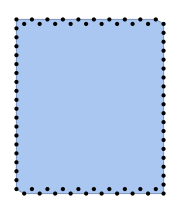

```mathematica
Show[{ConvexHullMesh[#],Graphics@Point[#]},ImageSize-> Small]&[Part[Values[ptsp],bcells]]
```

```mathematica
(* lets specify some limits for the boundaries *)
```

```mathematica
xLim={0.,13.50};
yLim={0.20,15.65};
```

```mathematica
Graphics3D[{
{Blue,Opacity[0.1],Polyhedron@Map[Lookup[indToPtsAssoc,#]&,cellVertexGrouping[#],{2}]&/@bcells[[1;;20]]},
{Red,Opacity[0.25],InfinitePlane[{{xLim[[1]],0,0},{xLim[[1]],1,0},{xLim[[1]],1,1}}]},
{Blue,Opacity[0.1],Polyhedron@Map[Lookup[indToPtsAssoc,#]&,cellVertexGrouping[#],{2}]&/@bcells[[-20;;]]},
{Red,Opacity[0.25],InfinitePlane[{{xLim[[2]],0,0},{xLim[[2]],1,0},{xLim[[2]],1,1}}]},
{Blue,Opacity[0.1],Polyhedron@Map[Lookup[indToPtsAssoc,#]&,cellVertexGrouping[#],{2}]&/@First@bcellsH},
{Red,Opacity[0.25],InfinitePlane[{{0,yLim[[1]],0},{1,yLim[[1]],0},{1,yLim[[1]],1}}]},
{Blue,Opacity[0.1],Polyhedron@Map[Lookup[indToPtsAssoc,#]&,cellVertexGrouping[#],{2}]&/@Last@bcellsH},
{Red,Opacity[0.25],InfinitePlane[{{0,yLim[[2]],0},{1,yLim[[2]],0},{0,yLim[[2]],1}}]}
},ImageSize->400,PlotRange->{{-1,14},{-1,16},{-1.6,0.5}},ViewPoint->Above,Axes-> True]
```

-Graphics3D-

```mathematica
(* 
We need a transformation matrix for each flagged cell -> this can be obtained by subtracting pt coordinates from the boundary limits;
storage matrix needs to be created for each flagged cell -> nearest neighbour function to be used for pts that pass boundary limits; 
*)
```

```mathematica
(*we choose two boundaries to create a nearest function to stitch the opposite boundaries *)
nearestFunc=Nearest@DeleteDuplicates@Flatten[DeleteDuplicates@Flatten[
Map[Lookup[indToPtsAssoc,#]&,cellVertexGrouping[#],{2}],1]&/@Join[Range@cellNumX,Last@bcellsH],1]
```

NearestFunction[…]

```mathematica
With[{xlim2= xLim[[2]],ylim1= yLim[[1]],ylim2= yLim[[2]]},
periodicRules=
Dispatch[{{x_/;x≥xlim2,y_/;y≤ylim1,z_}:> First@nearestFunc[{x-xlim2,y+ylim2,z}],
{x_/;x≥xlim2,y__}:>First@nearestFunc[ {x-xlim2,y}],
{x_,y_/;y≤ylim1,z_}:> First@nearestFunc[{x,y+ylim2,z}]}];

transformRules=Dispatch[{{x_/;x≥xlim2,y_/;y≤ylim1,_}:> {xlim2,-ylim2,0.},
{x_/;x≥xlim2,y__}:>{xlim2,0.,0.},
{x_,y_/;y≤ylim1,z_}:> {0.,-ylim2,0.},
{___Real}:> {0.,0.,0.}
}];
{periodicRules,transformRules}
]
```

{Dispatch[…],Dispatch[…]}

```mathematica
With[{xlim2= xLim[[2]],ylim1= yLim[[1]],ylim2= yLim[[2]]},
Graphics3D[
{Function[ind,{
{Red,PointSize[0.01],Point/@(Map[Lookup[indToPtsAssoc,#]&,cellVertexGrouping[ind],{2}] /.periodicRules)}
}]/@Join[First@bcellsH,Range[cellNum-cellNumX +1,cellNum]],
{Blue,Opacity[0.1],Polyhedron@Map[Lookup[indToPtsAssoc,#]&,cellVertexGrouping[#],{2}]&/@Join[Range@cellNumX,Range[cellNum-cellNumX +1,cellNum],
First@bcellsH,Last@bcellsH]},
{Green,Opacity[0.15],InfinitePlane[{{0,0,0},{0,1,0},{0,1,1}}],InfinitePlane[{{xlim2,0,0},{xlim2,1,0},{xlim2,1,1}}],
InfinitePlane[{{0,ylim1,0},{1,ylim1,0},{1,ylim1,1}}],InfinitePlane[{{0,ylim2,0},{1,ylim2,0},{0,ylim2,1}}]}},
ImageSize->500,Axes-> True,PlotRange->{{-0.1,xlim2},{ylim1,ylim2},{-1.5,1.0}}
]
]
```

-Graphics3D-

```mathematica
(* here is one boundary cell (#383) wrapping around on the opposite side *)
```

```mathematica
exampleCell= 383;
Block[{cvg=cellVertexGrouping[exampleCell],tMat},
Print["wrapping coordinates around using nearest neighbours"];
Print[Map[Lookup[indToPtsAssoc,#]&,cvg,{2}]/.periodicRules//Graphics3D[{XYZColor[0,0,1,0.5],PointSize[0.015],#}]&@*Map[Point]];
tMat=(Map[Lookup[indToPtsAssoc,#]&,cvg,{2}]/.transformRules);
Print["wrapped coordinates transformed to geometrically correct positions"];
Print@Graphics3D[{{PointSize[0.030],Opacity[0.25],Red,Point/@Map[Lookup[indToPtsAssoc,#]&,cvg,{2}]},
{PointSize[0.02],Blue,Point/@((Map[Lookup[indToPtsAssoc,#]&,cvg,{2}]/.periodicRules )+tMat)}},
ImageSize->Medium];
]
```

wrapping coordinates around using nearest neighbours

-Graphics3D-

wrapped coordinates transformed to geometrically correct positions

-Graphics3D-

```mathematica
flaggedCells={1}~Join~First@bcellsH~Join~Range[cellNum-cellNumX +1,cellNum]
```

{1,21,41,61,81,101,121,141,161,181,201,221,241,261,281,301,321,341,361,381,382,383,384,385,386,387,388,389,390,391,392,393,394,395,396,397,398,399,400}

```mathematica
flaggedCellsTransPts = Function[ind,ind->(Map[Lookup[indToPtsAssoc,#]&,cellVertexGrouping[ind],{2}] /.transformRules)]/@flaggedCells;
flaggedCellsStoragePts=Function[ind,ind->(Map[Lookup[indToPtsAssoc,#]&,cellVertexGrouping[ind],{2}] /.periodicRules)]/@flaggedCells;
```

```mathematica
Graphics3D[{PointSize[0.012],XYZColor[0,0,1,0.33],
Map[Point,flaggedCellsStoragePts[[#,2]]&/@Range[Length@flaggedCells],{2}]},
ImageSize->500]
```

-Graphics3D-

```mathematica
AssociateTo[cellVertexGrouping,MapAt[ptsToIndAssoc,flaggedCellsStoragePts,{All,2,All,All}]];
```

```mathematica
Block[{exampleCell=21,pos},
pos=First@@Position[flaggedCellsTransPts,exampleCell];
Graphics3D[{{Green,Opacity[0.3],PointSize[0.024],Point/@#},
{Blue,Opacity[0.5],PointSize[0.012],Point/@(#+Values[flaggedCellsTransPts[[pos]]])}},
ImageSize->Medium]&[Map[Lookup[indToPtsAssoc,#]&,cellVertexGrouping[exampleCell],{2}]]
]
```

-Graphics3D-

```mathematica
faceListCoords =Map[indToPtsAssoc,cellVertexGrouping,{3}];
```

```mathematica
faceListCoords=Merge[{faceListCoords,<|flaggedCellsTransPts|>},Total];
faceListCoords = Values@faceListCoords;
```

```mathematica
plt=Graphics3D[{Directive[Opacity[0.5]],Thread[{col,Polyhedron@Flatten[#,1]&/@(triangulateFaces/@faceListCoords)}]},
ImageSize->Full,Axes-> True]
```

-Graphics3D-

```mathematica
(* the mesh above is complete and is wrapped around the boundaries to form an infinite sheet of cells *)
```

```mathematica
edges=DeleteDuplicatesBy[Flatten[(x↦Partition[#,2,1,1]&/@x)/@faceListCoords,2],Sort];(* mesh edges *)
```

```mathematica
indToPtsAssoc=AssociationThread[Range[Length@#],#]&[DeleteDuplicates[Flatten[faceListCoords,2]]];(* <| vertex_labels -> vertex_pts |> *)
```

```mathematica
ptsToIndAssoc=<|Reverse[Normal@indToPtsAssoc,2]|>;
(* <| vertex_pts -> vertex_labels |>*)
```

```mathematica
cellVertexGrouping=AssociationThread[Range[Length@#],#]&[Map[Lookup[ptsToIndAssoc,#]&,faceListCoords,{2}]];
(* <|cell -> {{face vertex labels ..} ..}|>*)
```

```mathematica
vertexToCell=GroupBy[
Reverse[Flatten[Thread/@MapAt[Union@*Flatten,Normal[cellVertexGrouping],{All,2}]],2],
First-> Last];
```

```mathematica
(* <| vertex -> neighbouring cells .. |> *)
```

```mathematica
(* no duplicate pts found within tiny δ's *)
```

```mathematica
DeleteCases[
Lookup[ptsToIndAssoc,#]&/@
With[{vals=Values@indToPtsAssoc},
With[{nearest=Nearest[vals]},
nearest[#,{2,1.0 10^-15}]&/@vals
]
],x_/;Length[x]==1]//Length
```

0

```mathematica
Count[ Lookup[ptsToIndAssoc,#]&/@
With[{vals=DeleteDuplicates@Flatten[edges,1]},
With[{nf=Nearest@vals},
nf[#,{2,1.0 10^-15}]&/@vals
]
],{Repeated[_Integer,{2,∞}]}]
```

0

```mathematica
Length[
With[{vals=DeleteDuplicates@Flatten[edges,1]},
With[{nf=Nearest@vals},
nf[#,{2,1.0 10^-15}]&/@vals
]
]~DeleteCases~{{___Real}}
]
```

0

# Adding noise to mesh

## Import Mesh

```mathematica
DumpGet["C:\\Users\\aliha\\Desktop\\wolfram-vertex-3D\\create geometry\\infinitesheet.mx"];
yLim[[1]]=0.;
```

```mathematica
edges=SetPrecision[edges,10];
indToPtsAssoc=SetPrecision[indToPtsAssoc,10];
ptsToIndAssoc=KeyMap[SetPrecision[#,10]&,ptsToIndAssoc];
xLim=SetPrecision[xLim,10];
yLim=SetPrecision[yLim,10];
faceListCoords=Map[Lookup[indToPtsAssoc,#]&,cellVertexGrouping,{2}];
```

## Initialization/F[x]’s

```mathematica
With[{xlim1=xLim[[1]],xlim2= xLim[[2]],ylim1= yLim[[1]],ylim2= yLim[[2]]},
periodicRules=Dispatch[{
{x_/;x≥xlim2,y_/;y≤ylim1,z_}:> SetPrecision[{x-xlim2,y+ylim2,z},10],
{x_/;x≥xlim2,y_/;ylim1<y<ylim2,z_}:>SetPrecision[{x-xlim2,y,z},10],
{x_/;xlim1<x<xlim2,y_/;y≤ylim1,z_}:>SetPrecision[{x,y+ylim2,z},10],
{x_/;x<0.,y_/;y≤ylim1,z_}:>SetPrecision[{x+xlim2,y+ylim2,z},10],
{x_/;x<0.,y_/;ylim1<y<ylim2,z_}:>SetPrecision[{x+xlim2,y,z},10],
{x_/;x<0.,y_/;y>ylim2,z_}:>SetPrecision[{x+xlim2,y-ylim2,z},10],
{x_/;0.<x<xlim2,y_/;y>ylim2,z_}:>SetPrecision[{x,y-ylim2,z},10],
{x_/;x>xlim2,y_/;y≥ylim2,z_}:>SetPrecision[{x-xlim2,y-ylim2,z},10]
}];

transformRules=Dispatch[{
{x_/;x≥xlim2,y_/;y≤ylim1,_}:>SetPrecision[{-xlim2,ylim2,0},10],
{x_/;x≥xlim2,y_/;ylim1<y<ylim2,_}:>SetPrecision[{-xlim2,0,0},10],
{x_/;xlim1<x<xlim2,y_/;y≤ylim1,_}:>SetPrecision[{0,ylim2,0},10],
{x_/;x<0,y_/;y≤ylim1,_}:>SetPrecision[{xlim2,ylim2,0},10],
{x_/;x<0,y_/;ylim1<y<ylim2,_}:>SetPrecision[{xlim2,0,0},10],
{x_/;x<0,y_/;y>ylim2,_}:>SetPrecision[{xlim2,-ylim2,0},10],
{x_/;0<x<xlim2,y_/;y>ylim2,_}:>SetPrecision[{0,-ylim2,0},10],
{x_/;x>xlim2,y_/;y≥ylim2,_}:>SetPrecision[{-xlim2,-ylim2,0},10],
{___Real}:>SetPrecision[{0,0,0},10]}];
];
```

```mathematica
wrappedMat=AssociationThread[Keys[cellVertexGrouping]-> Map[Lookup[indToPtsAssoc,#]/.periodicRules&,
Lookup[cellVertexGrouping,Keys[cellVertexGrouping]],{2}]];
```

```mathematica
triangulateFaces[faces_]:=Block[{edgelen,ls,mean},
(ls=Partition[#,2,1,1];
edgelen=Norm[SetPrecision[First[#]-Last[#],10]]&/@ls;
mean=Total[edgelen*(Midpoint/@ls)]/Total[edgelen];
mean =mean~SetPrecision~10;
Map[Append[#,mean]&,ls])&/@faces
];
```

```mathematica
wrappedBoundaryPts[indptsassoc_,ptstoindassoc_]:=With[{xlim1=xLim[[1]],xlim2=xLim[[-1]],ylim1=yLim[[1]],ylim2=yLim[[-1]]},
Block[{pts,ptsxy,ptsx,ptsy,zmin,zmax,posx,negx,posy,negy,outsidePts,outsidePtscoords,shiftedpts},
pts=Values@indptsassoc;
ptsxy=pts[[All,1;;2]];
ptsx=ptsxy[[All,1]];
ptsy=ptsxy[[All,2]];
{zmin,zmax}=MinMax@pts[[All,-1]];
posx=Position[UnitStep[ptsx-xlim2],1];
negx=Position[ptsx,x_/;x<xlim1];
posy=Position[UnitStep[ptsy-ylim2],1];
negy=Position[ptsy,y_/;y<ylim1];
outsidePts=Union@Flatten[posx~Append~negx~Append~posy~Append~negy];
outsidePtscoords=Lookup[indptsassoc,outsidePts];

shiftedpts=Map[
Block[{tempvec=#},
tempvec=Which[tempvec[[1]]≥ xlim2,
{tempvec[[1]]-xlim2,tempvec[[2]],tempvec[[-1]]}~SetPrecision~10,
tempvec[[1]]< xlim1,
{tempvec[[1]]+xlim2,tempvec[[2]],tempvec[[-1]]}~SetPrecision~10,True,tempvec];
tempvec=Which[tempvec[[2]]≥ylim2,
{tempvec[[1]],tempvec[[2]]-ylim2,tempvec[[-1]]}~SetPrecision~10,
tempvec[[2]]< ylim1,
{tempvec[[1]],tempvec[[2]]+ylim2,tempvec[[-1]]}~SetPrecision~10,True,tempvec]
]&,outsidePtscoords];
Thread[{outsidePtscoords,Lookup[indptsassoc,Lookup[ptstoindassoc,shiftedpts]]}]
]
];
```

```mathematica
displaceVertices[indToPtsAssoc_,stitchedPtsInds_,cellVertexGrouping_,stdDev_:0.01]:=Block[{noiseFunc,lenstitchedPtsInds,unstitchedptsInds,
newunstitchedpts,newunstitchedindtopts,newstitchedindtopts,$indToPtsAssoc,$ptsToIndAssoc,$edges,$faceListCoords,$wrappedMat},
noiseFunc[μ_,σ_,n_]:= RandomVariate[NormalDistribution[μ,σ],{n,3}];
lenstitchedPtsInds=Length@stitchedPtsInds;
unstitchedptsInds=Complement[Keys@indToPtsAssoc,Flatten@stitchedPtsInds];
newunstitchedpts=SetPrecision[Lookup[indToPtsAssoc,unstitchedptsInds]+noiseFunc[0.,stdDev,Length@unstitchedptsInds],10];
newunstitchedindtopts=Thread[unstitchedptsInds->newunstitchedpts];
newstitchedindtopts=MapThread[(x↦x->SetPrecision[Lookup[indToPtsAssoc,x]+ #2,10])/@#1&,
{stitchedPtsInds,noiseFunc[0.,stdDev,lenstitchedPtsInds]}];
$indToPtsAssoc=KeySort@<|newunstitchedindtopts~Join~newstitchedindtopts|>;
$ptsToIndAssoc=AssociationMap[Reverse,$indToPtsAssoc];
$faceListCoords=Map[Lookup[$indToPtsAssoc,#]&,cellVertexGrouping,{2}];
$wrappedMat=AssociationThread[Keys[cellVertexGrouping]-> Map[Lookup[$indToPtsAssoc,#]/.periodicRules&,
Lookup[cellVertexGrouping,Keys[cellVertexGrouping]],{2}]];
$edges =Flatten[Map[Partition[#,2,1,1]&,Map[Lookup[$indToPtsAssoc,#]&,Values[cellVertexGrouping],{2}],{2}],2]//DeleteDuplicatesBy[Sort];
{$indToPtsAssoc,$ptsToIndAssoc,$faceListCoords,$wrappedMat,$edges}
];
```

```mathematica
𝒟=Rectangle[{First@xLim,First@yLim},{Last@xLim,Last@yLim}];
```

```mathematica
getLocalTopology[ptsToIndAssoc_,indToPtsAssoc_,vertexToCell_,cellVertexGrouping_,wrappedMat_,faceListCoords_][vertices_]:=Module[{localtopology=<||>,wrappedcellList={},vertcellconns,localcellunion,vertInBounds,v,wrappedcellpos,vertcs=vertices,
transVector,wrappedcellCoords,wrappedcells,vertOutofBounds,shiftedPt,transvecList={},$faceListCoords=Values@faceListCoords,
vertexQ},
vertexQ=MatchQ[vertices,{__?NumberQ}];
If[vertexQ,
vertcellconns=AssociationThread[{#} ,{vertexToCell[ptsToIndAssoc[#]]}]&@vertices;
vertcs={vertices};
localcellunion=Flatten[Values@vertcellconns],
(* this will yield vertex -> cell indices connected in the local mesh *)
vertcellconns=AssociationThread[# ,Lookup[vertexToCell,Lookup[ptsToIndAssoc,#]]]&@vertices; 
localcellunion=Union@Flatten[Values@vertcellconns];
];
(* condition to be an internal edge: both vertices should have 3 or more neighbours *)
(*Print["All topology known"];*)
(* the cells in the local mesh define the entire network topology -> no wrapping required *)
(* else cells need to be wrapped because other cells are connected to the vertices -> periodic boundary conditions *)
With[{vert=#},
If[((𝒟~RegionMember~Most[vert]) &&!(vert[[1]]== xLim[[2]]||vert[[2]]== yLim[[2]])),
(* the vertex has less than 3 neighbouring cells but the vertex is within bounds *)
(*Print["vertex inside bounds with fewer than 3 cells"];*)
v=vertInBounds=vert;
(* find cell indices that are attached to the vertex in wrappedMat *)
wrappedcellpos=DeleteDuplicatesBy[
Cases[Position[wrappedMat,x_/;SameQ[x,v],{3}],
{Key[p:Except[Alternatives@@Join[localcellunion,Flatten@wrappedcellList]]],y__}:>{p,y}],
First];
(*wrappedcellpos = wrappedcellpos/.{Alternatives@@Flatten[wrappedcellList],__} :> Sequence[];*)
(* if a wrapped cell has not been considered earlier (i.e. is new) then we translate it to the position of the vertex *)
If[wrappedcellpos≠{},
If[vertexQ,
transVector=SetPrecision[(v-Extract[$faceListCoords,Replace[#,{p_,q__}:> {Key[p],q},{1}]])&/@wrappedcellpos,10],
(*the main function is enquiring an edge and not a vertex*)
transVector=SetPrecision[(v-Extract[$faceListCoords,#])&/@wrappedcellpos,10]
];
wrappedcellCoords=MapThread[#1 -> Map[Function[x,SetPrecision[x+#2,10]],$faceListCoords[[#1]],{2}]&,
{First/@wrappedcellpos,transVector}];
wrappedcells= Keys@wrappedcellCoords;
AppendTo[wrappedcellList,Flatten@wrappedcells];
AppendTo[transvecList,transVector];
AppendTo[localtopology,wrappedcellCoords]; (*local topology here only has wrapped cell *)
],
(*Print["vertex out of bounds"];*)
(* else vertex is out of bounds *)
vertOutofBounds=vert;
(* translate the vertex back into mesh *)
transVector=vertOutofBounds/.transformRules;
shiftedPt= SetPrecision[vertOutofBounds+transVector,10];
(* find which cells the vertex is a part of in the wrapped matrix *)
wrappedcells=Complement[
Union@Cases[Position[wrappedMat,x_/;SameQ[x,shiftedPt],{3}],
x_Key:>Sequence@@x,{2}]/.Alternatives@@localcellunion-> Sequence[],
Flatten@wrappedcellList];
(*forming local topology now that we know the wrapped cells *)
If[wrappedcells≠{},
AppendTo[wrappedcellList,Flatten@wrappedcells];
wrappedcellCoords=AssociationThread[wrappedcells,
Map[Lookup[indToPtsAssoc,#]&,cellVertexGrouping[#]&/@wrappedcells,{2}]
];
With[{opt=(vertOutofBounds/.periodicRules)},
Block[{pos,vertref,transvec},
Do[
With[{cellcoords=wrappedcellCoords[cell]},
pos=FirstPosition[cellcoords/.periodicRules,opt];
vertref=Extract[cellcoords,pos];
transvec=SetPrecision[vertOutofBounds-vertref,10];
AppendTo[transvecList,transvec];
AppendTo[localtopology,cell-> Map[SetPrecision[#+transvec,10]&,cellcoords,{2}]];
],{cell,wrappedcells}]
];
];
];
];
]&/@vertcs;
If[localcellunion≠ {},
AppendTo[localtopology,
Thread[localcellunion->Map[Lookup[indToPtsAssoc,#]&,cellVertexGrouping/@localcellunion,{2}]]
]
];
(*Print[Values@localtopology//Min/@Map[Precision,#,{3}]&];*)
transvecList=Which[
MatchQ[transvecList,{{{__?NumberQ}}}],First[transvecList],
MatchQ[transvecList,{{__?NumberQ}..}],transvecList,
True,transvecList//.{x___,{p:{__?NumberQ}..},y___}:>{x,p,y}
];
{localtopology,Flatten@wrappedcellList,transvecList}
];
```

## Addition of noise

```mathematica
outsideptspairs=wrappedBoundaryPts[indToPtsAssoc,ptsToIndAssoc];
mappedpts=GroupBy[#~Join~Reverse[#,2]&@(Rule@@Lookup[ptsToIndAssoc,#]&/@outsideptspairs),First-> Last];
```

```mathematica
stitchedPtsInds=Block[{wrapI,bpconn,val,temp,keys=Keys@mappedpts},
ParallelTable[
wrapI={i};
bpconn=First@FixedPoint[
(val=#[[-1]];
temp=Flatten[Lookup[mappedpts,#]&@val];
wrapI=If[Complement[temp,#1[[1]]]≠{},Union@Flatten@Append[wrapI,temp],wrapI];
{wrapI,temp})&,{wrapI,wrapI},SameTest->(#[[1]]===#2[[1]]&)],{i,keys}]
]//DeleteDuplicatesBy[Sort];
```

```mathematica
bpts=Union@Flatten@stitchedPtsInds;
innerptsInds=Complement[Keys@indToPtsAssoc,bpts];
```

```mathematica
SeedRandom[3];
{$indToPtsAssoc,$ptsToIndAssoc,$faceListCoords,$wrappedMat,$edges}=displaceVertices[indToPtsAssoc,stitchedPtsInds,cellVertexGrouping,0.05];
```

```mathematica
$wrappedMatTrim=KeyTake[$wrappedMat,Union@Flatten[vertexToCell/@bpts,1]];
```

```mathematica
(problematicidx=Flatten@Position[Keys[getLocalTopology[$ptsToIndAssoc,$indToPtsAssoc,vertexToCell,cellVertexGrouping,$wrappedMatTrim,$faceListCoords][$indToPtsAssoc[#]]//First]&/@bpts//Map[Length],_?(#<3&)])=={}
```

True

```mathematica
mesh=Map[Lookup[$indToPtsAssoc,#]&,cellVertexGrouping,{2}];
```

```mathematica
Graphics3D[Polyhedron@Flatten[triangulateFaces@#,1]&/@Values[mesh]]
```

-Graphics3D-

```mathematica
(*Manipulate[Graphics3D[{Polyhedron@Flatten[triangulateFaces@#,1]&/@Values[mesh],PointSize[0.02],Red,Point@$indToPtsAssoc[#]&/@bpts[[problemidx]],
PointSize[0.01],Green,Point@$indToPtsAssoc[#]&/@Complement[bpts,bpts[[problemidx]]],PointSize[0.02],Black,Dynamic[Point@$indToPtsAssoc[i]]},ImageSize->Large],{i,1,Length[Keys@$indToPtsAssoc],1}]*)
```

all boundary vertices should have 3 neighbours

```mathematica
Keys[getLocalTopology[$ptsToIndAssoc,$indToPtsAssoc,vertexToCell,cellVertexGrouping,$wrappedMatTrim,$faceListCoords][$indToPtsAssoc[#]]//First]&/@bpts//Counts@*Map[Length]
```

<|3→316|>

all vertices should have 3 neighbours

```mathematica
Keys[getLocalTopology[$ptsToIndAssoc,$indToPtsAssoc,vertexToCell,cellVertexGrouping,$wrappedMatTrim,$faceListCoords][$indToPtsAssoc[#]]//First]&/@Range[Max@$ptsToIndAssoc]//Counts@*Map[Length]
```

<|3→1760|>

```mathematica
Graphics3D[{{Opacity[0.2],Polyhedron/@Values[getLocalTopology[$ptsToIndAssoc,$indToPtsAssoc,vertexToCell,cellVertexGrouping,$wrappedMatTrim,$faceListCoords][$indToPtsAssoc[#]]//First]},{Red,PointSize[0.05],Point@$indToPtsAssoc[#]}},ImageSize->Tiny]&[RandomChoice@*Range@*Max@$ptsToIndAssoc]
```

-Graphics3D-

```mathematica
(*Manipulate[Graphics3D[{{Opacity[0.2],Polyhedron/@Values[getLocalTopology[$ptsToIndAssoc,$indToPtsAssoc,vertexToCell,cellVertexGrouping,$wrappedMat,$faceListCoords][$indToPtsAssoc[i]]//First]},{Red,PointSize[0.03],Point@$indToPtsAssoc[i]}}],{i,1,Length@indToPtsAssoc,1}]*)
```

## Exporting Mesh

Export the new mesh and all of the associated data-structures

```mathematica
(*{edges,indToPtsAssoc,ptsToIndAssoc,wrappedMat,faceListCoords}={$edges,$indToPtsAssoc,$ptsToIndAssoc,$wrappedMat,$faceListCoords};
DumpSave["C:\\Users\\aliha\\Desktop\\wolfram-vertex-3D\\add noise to mesh\\infinitesheet-noise.mx",{edges,indToPtsAssoc,ptsToIndAssoc,vertexToCell,cellVertexGrouping,wrappedMat,faceListCoords,xLim,yLim}];*)
```